```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Run simulation, collect data and export *)
{Δc1,Δc2,U1,U2,popsize,starttime,timestep,maxtime}={0.01,0.01,1 10^-4,1 10^-4,10^6,0,1000,20000};
{verbose,veryverbose,fulldata,setseed}={False,False,0,7};
(* Check Regimes *)
printRegimeDetails[Δc1,Δc2,U1,U2,popsize];
{genotypes,genotypeabundances}=getInitial2Ddistribution[5,popsize,Δc1,Δc2,U1,U2];
```

```mathematica
SeedRandom[setseed];
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-10p10_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp001.m",results];
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Export plots of symmetric evolution *)
results=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p10_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp001.m"];
meansubload=Mean[Table[results[[i]][[9]],{i,1,Length[results]}]];
timesAndLoads=Table[{results[[i]][[1]],results[[i]][[9]]},{i,Length[results]}];
timesAndMean1=Table[{results[[i]][[1]],results[[i]][[2]]},{i,1,Length[results]}];
timesAndMean2=Table[{results[[i]][[1]],results[[i]][[3]]},{i,1,Length[results]}];
timesAndVar1=Table[{results[[i]][[1]],results[[i]][[6]]},{i,1,Length[results]}];
timesAndVar2=Table[{results[[i]][[1]],results[[i]][[7]]},{i,1,Length[results]}];
timesAndCov=Table[{results[[i]][[1]],results[[i]][[5]]},{i,1,Length[results]}];
mean2mean=Table[{results[[i]][[2]]/Δc1,results[[i]][[3]]/Δc2},{i,1,Length[results]}];
noseTravel=Table[results[[i]][[12]],{i,1,Length[results]}];
Export["~Documents/kgrel2d/plots/timevsload_N-10p10_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp001.gif",
ListPlot[timesAndLoads,AxesLabel->{"Time","Substitutional Load"},PlotLabel->"Substitutional Load vs Time: mean load = "<>ToString[meansubload]]];
Export["~Documents/kgrel2d/plots/timevsmeans_N-10p10_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp001.gif",
ListPlot[{timesAndMean1,timesAndMean2},PlotStyle->{Blue,Red},PlotLegends->{"mean trait 1","mean trait 2"},AxesLabel->{"Time","mean fitness"},PlotLabel->"mean fitness vs Time"]];
Export["~Documents/kgrel2d/plots/timevsvariances_N-10p10_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp001.gif",
ListPlot[{timesAndVar1,timesAndVar2,timesAndCov},PlotStyle->{Blue,Red,Black},PlotLegends->{"variance trait 1","variance trait 2","covariance"},AxesLabel->{"Time","Variances"},PlotLabel->"Variances vs Time"]];
Export["~Documents/kgrel2d/plots/timevscovariance_N-10p10_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp001.gif",
ListPlot[{timesAndCov},PlotStyle->{Black},PlotLegends->{"variance trait 1","variance trait 2","covariance"},AxesLabel->{"Time","Variances"},PlotLabel->"mean covariance " <>ToString[Mean[timesAndCov[[;;,2]]]]]];
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Compute PDFs over relative fitness (very computationally intensive ) *)
results1=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p11_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp003.m"];
results2=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p10_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp002.m"];
PDF1vsTime=ParallelTable[{results1[[i]][[1]],getMeanPDF[{results1[[i]]}][[1]],getMeanPDF[{results1[[i]]}][[2]]},{i,1,Length[results1]}];
PDF2vsTime=ParallelTable[{results2[[i]][[1]],getMeanPDF[{results2[[i]]}][[1]],getMeanPDF[{results2[[i]]}][[2]]},{i,1,Length[results2]}];
Export["~/Documents/kgrel2d/data/simtest/PDF1vsTime_N-10p11_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp003.m",PDF1vsTime];
Export["~/Documents/kgrel2d/data/simtest/PDF2vsTime_N-10p10_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp002.m",PDF2vsTime];
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Transform PDFvsTime data to Matrix data *)
results1=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p11_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp003.m"];
results2=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p10_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp002.m"];
PDF1vsTime=Import["~/Documents/kgrel2d/data/simtest/PDF1vsTime_N-10p11_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp003.m"];
PDF2vsTime=Import["~/Documents/kgrel2d/data/simtest/PDF2vsTime_N-10p10_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp002.m"];
(* heatplot snapshot over various generations *)
trait1bound=Max[Abs[Min[Flatten[PDF1vsTime[[;;,2]]]]],Max[Flatten[PDF1vsTime[[;;,2]]]]];
heatplotdata1=ParallelTable[
heatdata=Array[0 #1 #2 &,{2trait1bound+1,2trait1bound+1}];
Do[heatdata[[trait1bound+1-PDF1vsTime[[i]][[2]][[j]][[1]],PDF1vsTime[[i]][[2]][[j]][[2]]+trait1bound+1]]=PDF1vsTime[[i]][[3]][[j]],{j,1,Length[PDF1vsTime[[i]][[2]]]}];
{PDF1vsTime[[i]][[1]],heatdata,results1[[i]][[4]]},{i,1,Length[PDF1vsTime]}];
Export["~/Documents/kgrel2d/data/simtest/heatplot_N-10p11_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp003.m",heatplotdata1];
trait2bound=Max[Abs[Min[Flatten[PDF2vsTime[[;;,2]]]]],Max[Flatten[PDF2vsTime[[;;,2]]]]];
heatplotdata2=ParallelTable[
heatdata=Array[0 #1 #2 &,{2trait2bound+1,2trait2bound+1}];
Do[heatdata[[trait2bound+1-PDF2vsTime[[i]][[2]][[j]][[1]],PDF2vsTime[[i]][[2]][[j]][[2]]+trait2bound+1]]=PDF2vsTime[[i]][[3]][[j]],{j,1,Length[PDF2vsTime[[i]][[2]]]}];
{PDF2vsTime[[i]][[1]],heatdata,results2[[i]][[4]]},{i,1,Length[PDF2vsTime]}];
Export["~/Documents/kgrel2d/data/simtest/heatplot_N-10p10_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp002.m",heatplotdata2];
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Create Plots with matrix data *)
heatplotdata1=Import["~/Documents/kgrel2d/data/simtest/heatplot_N-10p11_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp003.m"];
heatplotdata2=Import["~/Documents/kgrel2d/data/simtest/heatplot_N-10p10_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp002.m"];
(* generate snapshots of distribution over time *)
ParallelDo[
Export["~/Documents/kgrel2d/plots/simplots1/heatplot_N-10p11_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp"<>ToString[i]<>".jpg",MatrixPlot[Log10[heatplotdata1[[100i]][[2]]],PlotLabel->"t="<>ToString[heatplotdata1[[100i]][[1]]]<>", mean="<>ToString[(heatplotdata1[[100i]][[3]]-{1,1})*{Δc1^-1,Δc2^-1}],PlotLegends->Automatic]]
,{i,1,Floor[Length[heatplotdata1]/100]}];
ParallelDo[
Export["~/Documents/kgrel2d/plots/simplots2/heatplot_N-10p10_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp"<>ToString[i]<>".jpg",
MatrixPlot[Log10[heatplotdata2[[100i]][[2]]],PlotLabel->"t="<>ToString[heatplotdata2[[100i]][[1]]]<>", mean="<>ToString[(heatplotdata2[[100i]][[3]]-{1,1})*{Δc1^-1,Δc2^-1}],PlotLegends->Automatic]]
,{i,1,Floor[Length[heatplotdata2]/100]}];
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Create Plots with matrix data *)
heatplotdata1=Import["~/Documents/kgrel2d/data/simtest/heatplot_N-10p11_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp003.m"];
heatplotdata2=Import["~/Documents/kgrel2d/data/simtest/heatplot_N-10p10_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp002.m"];
offset=2000;
(* generate snapshots of distribution over time *)
ParallelDo[
Export["~/Documents/kgrel2d/plots/simplots1/short/heatplot_N-10p11_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp"<>ToString[i]<>".jpg",MatrixPlot[Log10[heatplotdata1[[i+offset]][[2]]],PlotLabel->"t="<>ToString[heatplotdata1[[i+offset]][[1]]]<>", mean="<>ToString[(heatplotdata1[[i+offset]][[3]]-{1,1})*{Δc1^-1,Δc2^-1}],PlotLegends->Automatic]]
,{i,1,100}];
ParallelDo[
Export["~/Documents/kgrel2d/plots/simplots2/short/heatplot_N-10p10_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp"<>ToString[i]<>".jpg",
MatrixPlot[Log10[heatplotdata2[[i+offset]][[2]]],PlotLabel->"t="<>ToString[heatplotdata2[[i+offset]][[1]]]<>", mean="<>ToString[(heatplotdata2[[i+offset]][[3]]-{1,1})*{Δc1^-1,Δc2^-1}],PlotLegends->Automatic]]
,{i,1,100}];
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Plot contours of mean PDF*)
meanPDF1=Import["~/Documents/kgrel2d/data/simtest/meanPDF_N-10p11_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp003.m"];
meanPDF1=Import["~/Documents/kgrel2d/data/simtest/meanPDF_N-10p10_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp003.m"];
meanPDF1[[2]]=(1/Total[meanPDF1[[2]]])meanPDF1[[2]];
meanPDF2[[2]]=(1/Total[meanPDF2[[2]]])meanPDF2[[2]];
pdfsurf1=Table[{meanPDF1[[1]][[i]][[1]],meanPDF1[[1]][[i]][[2]],Log[meanPDF1[[2]][[i]]]},{i,1,Length[meanPDF1[[1]]]}];
pdfsurf2=Table[{meanPDF2[[1]][[i]][[1]],meanPDF2[[1]][[i]][[2]],Log[meanPDF2[[2]][[i]]]},{i,1,Length[meanPDF2[[1]]]}];
Export["~/Documents/kgrel2d/plots/meanPDF_N-10p11_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp003.pdf",ListContourPlot[pdfsurf1,PlotRange->All,PlotLegends->Automatic]];
Export["~/Documents/kgrel2d/plots/meanPDF_N-10p10_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp003.pdf",ListContourPlot[pdfsurf2,PlotRange->All,PlotLegends->Automatic]];
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check evolution (specifically covariance in 2 dimensions and store full data *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.01,1 10^-4,1 10^-4,10^11};
{starttime,timestep,maxtime}={0,1000,50000}; 
{fulldata,verbose,veryverbose,exactqv}={1,False,False,True};
(* Check Regimes *)
printRegimeDetails[Δc1,Δc2,U1,U2,popsize,exactqv];
(* Set initial genotypes and their abundances *)
{genotypes,genotypeabundances}=getInitial2Ddistribution[3,popsize,Δc1,Δc2,U1,U2];
```

Trait 1 q = 10.4053 in Concurrent Mutations Regime with expected time scale 48.9634 and rate of adaptation 0.000204234

Trait 2 q = 10.4053 in Concurrent Mutations Regime with expected time scale 48.9634 and rate of adaptation 0.000204234

```mathematica
(* Run simulation *)
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-10p11_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp004.m",results];
```

```mathematica
getMeanPDF[results_]:=Module[{truepopsize,trait1mean,trait2mean,meanPDF,matchflag},
(* initialize local variables *)
meanPDF={{},{}};
matchflag=False;

Do[ (* Loop through all possible results *)
truepopsize = Total[results[[i]][[3]]];
trait1mean=Round[results[[i]][[4]][[1]]];
trait2mean=Round[results[[i]][[4]][[2]]];

Do[ (* For each result run through current list in meanPDF, check if fit.class present, then add abundance or update *)
Do[ (* Run through list of current meanPDF *)
If[Length[meanPDF[[1]]]==0,
meanPDF[[1]]=Join[meanPDF[[1]],{results[[i]][[2]][[k]]-{trait1mean,trait2mean}}];
meanPDF[[2]]=Join[meanPDF[[2]],{(1/truepopsize)results[[i]][[3]][[k]]}];,
If[meanPDF[[1]][[l]]==(results[[i]][[2]][[k]]-{trait1mean,trait2mean}),
meanPDF[[2]][[l]]+=(1/truepopsize)results[[i]][[3]][[k]]; matchflag=True;];];
,{l,1,Max[1,Length[meanPDF[[1]]]]}];
If[!matchflag,
meanPDF[[1]]=Join[meanPDF[[1]],{results[[i]][[2]][[k]]-{trait1mean,trait2mean}}];
meanPDF[[2]]=Join[meanPDF[[2]],{(1/truepopsize)results[[i]][[3]][[k]]}];,matchflag=False];
,{k,1,Length[results[[i]][[2]]]}];
,{i,1,Length[results]}];
meanPDF
]
```

```mathematica
results1=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p11_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp003.m"];
results2=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p11_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp004.m"];
meanPDF1=getMeanPDF[results1];
meanPDF2=getMeanPDF[results2];
Export["~/Documents/kgrel2d/data/simtest/meanPDF_N-10p11_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp003.m",meanPDF1];
Export["~/Documents/kgrel2d/data/simtest/meanPDF_N-10p11_c1-0d01_c2-0d01_U1-1x10pn4_U2-1x10pn4_exp004.m",meanPDF2];
```

```mathematica
meanPDF1[[2]]=(1/Total[meanPDF1[[2]]])meanPDF1[[2]];
meanPDF2[[2]]=(1/Total[meanPDF2[[2]]])meanPDF2[[2]];
```

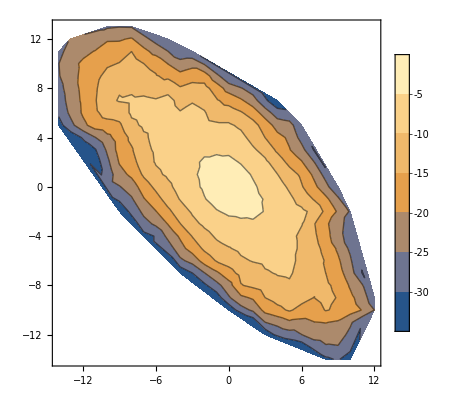

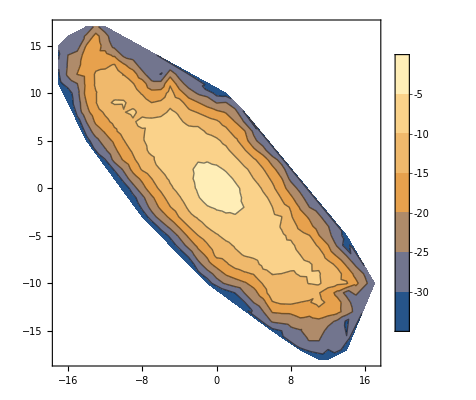

```mathematica
pdfsurf1=Table[{meanPDF1[[1]][[i]][[1]],meanPDF1[[1]][[i]][[2]],Log[meanPDF1[[2]][[i]]]},{i,1,Length[meanPDF1[[1]]]}];
pdfsurf2=Table[{meanPDF2[[1]][[i]][[1]],meanPDF2[[1]][[i]][[2]],Log[meanPDF2[[2]][[i]]]},{i,1,Length[meanPDF2[[1]]]}];
ListContourPlot[pdfsurf1,PlotLegends->Automatic]
ListContourPlot[pdfsurf2,PlotLegends->Automatic]
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check evolution (specifically covariance in 2 dimensions and store full data *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.01,1 10^-5,1 10^-5,10^11};
{starttime,timestep,maxtime}={0,1000,30000}; 
{fulldata,verbose,veryverbose,exactqv}={1,False,False,True};
(* Check Regimes *)
printRegimeDetails[Δc1,Δc2,U1,U2,popsize,exactqv];
(* Set initial genotypes and their abundances *)
{genotypes,genotypeabundances}=getInitial2Ddistribution[3,popsize,Δc1,Δc2,U1,U2];
```

Trait 1 q = 6.83154 in Concurrent Mutations Regime with expected time scale 118.455 and rate of adaptation 0.0000844201

Trait 2 q = 6.83154 in Concurrent Mutations Regime with expected time scale 118.455 and rate of adaptation 0.0000844201

```mathematica
(* Run simulation *)
SeedRandom[16];
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-10p11_c1-0d01_c2-0d01_U1-1x10pn5_U2-1x10pn5_exp005.m",results];
```

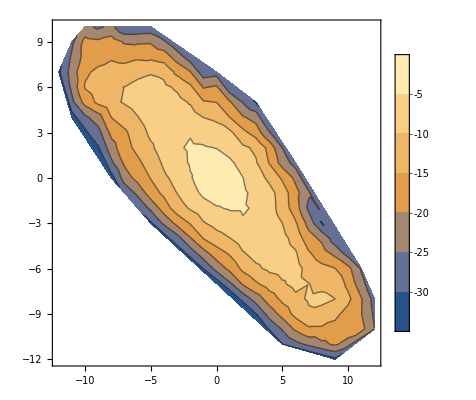

```mathematica
meanPDF3=getMeanPDF[results];
Export["~/Documents/kgrel2d/data/simtest/meanPDF_N-10p11_c1-0d01_c2-0d01_U1-1x10pn5_U2-1x10pn5_exp003.m",meanPDF3];
meanPDF3[[2]]=(1/Total[meanPDF3[[2]]])meanPDF3[[2]];
pdfsurf3=Table[{meanPDF3[[1]][[i]][[1]],meanPDF3[[1]][[i]][[2]],Log[meanPDF3[[2]][[i]]]},{i,1,Length[meanPDF3[[1]]]}];
ListContourPlot[pdfsurf3,PlotLegends->Automatic]
```

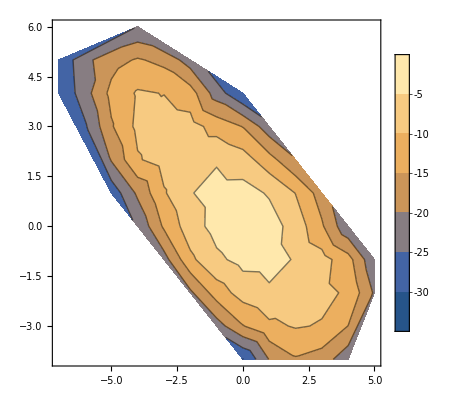

```mathematica
meanPDF3=getMeanPDF[results];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-10p11_c1-0d01_c2-0d01_U1-1x10pn7_U2-1x10pn7_exp006.m",meanPDF3];
meanPDF3[[2]]=(1/Total[meanPDF3[[2]]])meanPDF3[[2]];
pdfsurf3=Table[{meanPDF3[[1]][[i]][[1]],meanPDF3[[1]][[i]][[2]],Log[meanPDF3[[2]][[i]]]},{i,1,Length[meanPDF3[[1]]]}];
ListContourPlot[pdfsurf3,PlotLegends->Automatic]
```

```mathematica
({3,4}-{1,1})*{1/2,1/2}
```

{1,3/2}